```mathematica
Import["hb.csv","Table"]
```

Import::nffil: File not found during Import.

$Failed

```mathematica
t = Import["/Users/friedrich/Desktop/hb.csv","Table"]
```

{{0,7.04},{1.02,7.04},{2.12,7.04},{3.28,7.04},{4.37,7.05},{5.46,7.05},{6.55,7.06},{7.64,7.06},{8.73,7.06},{9.83,7.08},{10.8,7.08},{11.9,7.09},{12.8,7.11},{13.8,7.15},{14.6,7.16},{15.5,7.21},{16.9,7.29},{17.8,7.35},{18.5,7.44},{19.2,7.49},{19.9,7.58},{20.3,7.67},{20.9,7.73},{21.6,7.84},{22.4,7.87},{23,7.93},{23.8,7.87},{24.8,7.79},{25.5,7.58},{25.9,7.38},{26.4,7.07},{26.7,6.95},{26.9,6.81},{27.2,6.67},{27.5,6.54},{28,6.25},{28.2,6.09},{28.6,5.95},{28.9,5.81},{29.1,5.67},{29.4,5.54},{29.8,5.43},{30,5.26},{30.5,5.11},{30.9,4.97},{31.3,4.82},{31.8,4.59},{32.3,4.45},{32.9,4.28},{33.4,4.13},{33.9,4.02},{34.3,3.84},{34.8,3.76},{35.1,3.64},{35.7,3.5},{36.4,3.41},{37.4,3.3},{37.8,3.13},{38.5,3.07},{39.5,2.95},{40.4,2.84},{41.6,2.75},{42.4,2.64},{43.5,2.61},{44.1,2.52},{44.8,2.48},{45.5,2.45},{46.3,2.41},{47,2.38},{48.1,2.34}}

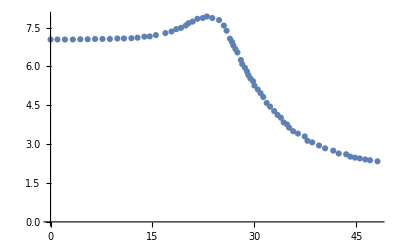

```mathematica
ListPlot[t]
```

```mathematica
f = LinearModelFit[t,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10,x^11,x^12,x^13},x]
```

FittedModel[7.06231-0.362935 x+«15»+4.27014×10^-15 x^12+4.12342×10^-18 x^13]

```mathematica
f["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 7.06231 | 0.073186 | 96.4981 | 5.89483×10^-64
x | -0.362935 | 0.218831 | -1.65851 | 0.102805
x^2 | 0.4128 | 0.197973 | 2.08514 | 0.0416272
x^3 | -0.174946 | 0.0774787 | -2.25799 | 0.0278625
x^4 | 0.0377169 | 0.016534 | 2.28117 | 0.0263628
x^5 | -0.00473409 | 0.00216356 | -2.1881 | 0.032851
x^6 | 0.0003715 | 0.000185427 | 2.00348 | 0.0499733
x^7 | -0.0000189184 | 0.0000108026 | -1.75128 | 0.0853727
x^8 | 6.33731×10^-7 | 4.35322×10^-7 | 1.45577 | 0.151039
x^9 | -1.38266×10^-8 | 1.214×10^-8 | -1.13893 | 0.259583
x^10 | 1.88175×10^-10 | 2.29981×10^-10 | 0.818219 | 0.4167
x^11 | -1.4294×10^-12 | 2.82429×10^-12 | -0.506108 | 0.614768
x^12 | 4.27014×10^-15 | 2.02773×10^-14 | 0.210588 | 0.833973
x^13 | 4.12342×10^-18 | 6.46048×10^-17 | 0.0638253 | 0.949337

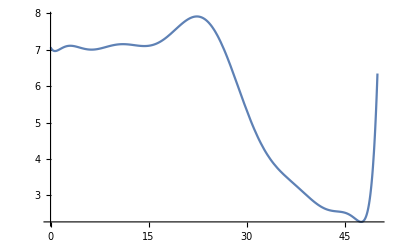

6.98652+0.389547 Parameters-0.310313 Parameters^2+0.0927043 Parameters^3-0.0137706 Parameters^4+0.00115273 Parameters^5-0.0000577053 Parameters^6+1.76479×10^-6 Parameters^7-3.2482×10^-8 Parameters^8+3.35512×10^-10 Parameters^9-1.59334×10^-12 Parameters^10+1.44128×10^-15 Parameters^11

```mathematica
Plot[f[x],{x,0,50}]
```